```mathematica
Exp[D[1/(1+Exp[-x]),x]/(1/(1+Exp[-x]))]
```

ⅇ^(ⅇ^-x/(1+ⅇ^-x))

```mathematica
Simplify[ⅇ^(ⅇ^-x/(1+ⅇ^-x))]
```

ⅇ^(1/(1+ⅇ^x))

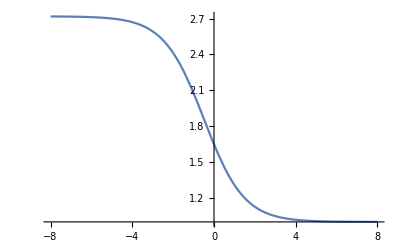

```mathematica
Plot[ⅇ^(1/(1+ⅇ^x)),{x,-8,8}]
```

```mathematica
D[f[x],x]==f[x]+2f[x]+3f[x]
```

f'[x]==6 f[x]

```mathematica
DSolve[f'[x]==6 f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(6 x) C[1]}}

```mathematica
D[x^2,x]
```

2 x

```mathematica
D[f[x],x]==2 f[x]/x
```

f'[x]==(2 f[x])/x

```mathematica
DSolve[f'[x]==(2 f[x])/x,{f[x]},{x}]
```

{{f[x]→x^2 C[1]}}

```mathematica
D[f[x],x]==α f[x]/x
```

f'[x]==(α f[x])/x

```mathematica
DSolve[f'[x]==(α f[x])/x,{f[x]},{x}]
```

{{f[x]→x^α C[1]}}

```mathematica
1/x
```

1/x

```mathematica
D[1/x, x]
```

-1/x^2

```mathematica
D[f[x], x]==-f[x]^2
```

f'[x]==-f[x]^2

```mathematica
DSolve[f'[x]==-f[x]^2,{f[x]},{x}]
```

{{f[x]→1/(x-C[1])}}

```mathematica
D[f[x],x]==1/(1+f[x])
```

f'[x]==1/(1+f[x])

```mathematica
DSolve[f'[x]==1/(1+f[x]),{f[x]},{x}]
```

{{f[x]→-1-√(1+2 x+2 C[1])},{f[x]→-1+√(1+2 x+2 C[1])}}

```mathematica
D[f[x],x]==1/(1+1/(1+f[x]))
```

f'[x]==1/(1+1/(1+f[x]))

```mathematica
DSolve[f'[x]==1/(1+1/(1+f[x])),{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→-1+ProductLog[ⅇ^(1+x+C[1])]}}

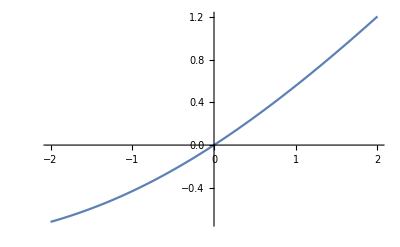

```mathematica
Plot[ProductLog[ⅇ^(1+x)]-1,{x,-2,2}]
```

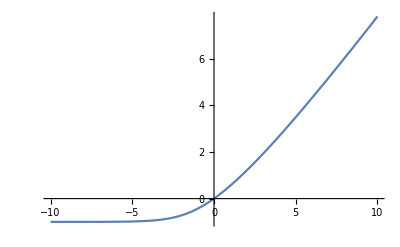

```mathematica
Plot[ProductLog[ⅇ^(1+x)]-1,{x,-10,10}]
```

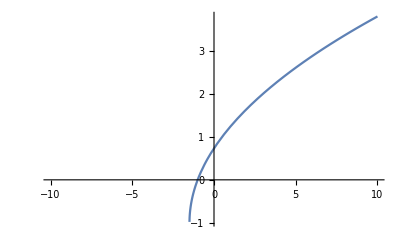

```mathematica
Plot[√(1+2 x+2)-1,{x,-10,10}]
```

```mathematica
Hold[Integrate[√(1+f'[x]),{x,a,b}]]
```

Hold[∫_a^b √(1+f'[x])ⅆx]

```mathematica
∫_a^b √(1+f'[x])ⅆx
```

∫_a^b √(1+f'[x])ⅆx

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],x∈Reals]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f'[x],f''[x]}∈Reals]
```

Abs[f''[x]]/((1+f'[x]^2)^(3/2))

```mathematica
∫_a^b √(1+f'[x]^2)ⅆx
```

∫_a^b √(1+f'[x]^2)ⅆx

```mathematica
With[{f=#^2&},
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f'[x],f''[x]}∈Reals]
]
```

2/((1+4 x^2)^(3/2))

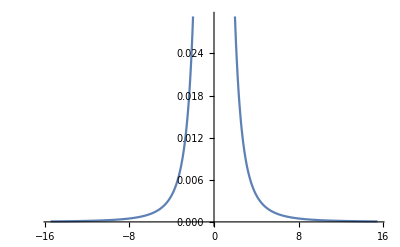

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

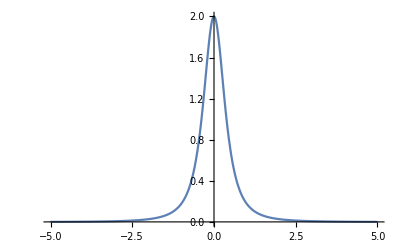

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-5,5},PlotRange->Full]
```

```mathematica
Integrate[2/((1+4 x^2)^(3/2)),{x,0,2}]
```

4/(√17)

```mathematica
Integrate[2/((1+4 x^2)^(3/2)),{x,0,1}]
```

2/(√5)

```mathematica
N[2/(√5)]
```

0.894427

```mathematica
Integrate[√(1+4 x^2),{x,0,1}]
```

1/4 (2 √5+ArcSinh[2])

```mathematica
N[1/4 (2 √5+ArcSinh[2])]
```

1.47894

```mathematica
ArcLength[{x,x^2},{x,0,1}]
```

1/4 (2 √5+ArcSinh[2])

```mathematica
ArcLength[{x,f[x]},{x,0,1}]
```

∫_0^1 √(1+f'[x]^2)ⅆx

```mathematica
SurfaceArea[Sin[x y]]
```

SurfaceArea::reg: Sin[x y] is not a correctly specified region.

SurfaceArea[Sin[x y]]

```mathematica
SurfaceArea[ImplicitRegion[x^2+y^2+z^2≤1,{x,y,z}]]
```

4 π

```mathematica
Area[Sphere[]]
```

4 π

```mathematica
Disk[]
```

Disk[{0,0}]

```mathematica
Area[Sin[x y],{x,0,1},{y,0,1}]
```

∫_0^1 ∫_0^1 √(1+(x^2+y^2) Cos[x y]^2)ⅆyⅆx

```mathematica
SurfaceArea[ImplicitRegion[Sin[x y]≤1,{x,y}]]
```

Undefined

```mathematica
SurfaceArea[ImplicitRegion[x^2+y^2+z^2≤1,{x,y,z}]]
```

4 π

```mathematica
SurfaceArea[ImplicitRegion[Sin[x y]≤1,{x,y}]]
```

Undefined

```mathematica
SurfaceArea[ImplicitRegion[Sin[x y]<1,{x,y}]]
```

Undefined

```mathematica
ImplicitRegion[Sin[x y]∧x^2+y^2<1,{x,y}]
```

ImplicitRegion::bcond: Sin[x y]&&x^2+y^2<1 should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion[Sin[x y]&&x^2+y^2<1,{x,y}]

```mathematica
ImplicitRegion[-1<Sin[x y]<1&&x^2+y^2<1,{x,y}]
```

ImplicitRegion[-1<Sin[x y]<1&&x^2+y^2<1,{x,y}]

```mathematica
SurfaceArea[ImplicitRegion[-1<Sin[x y]<1&&x^2+y^2<1,{x,y}]]
```

Undefined

```mathematica
ContourPlot3D[Sin[x y]==0,{x,y}∈Disk[]]
```

ContourPlot3D::idomdim: {x,y}∈Disk[] does not have a valid dimension as a plotting domain.

ContourPlot3D[Sin[x y]==0,{x,y}∈Disk[]]

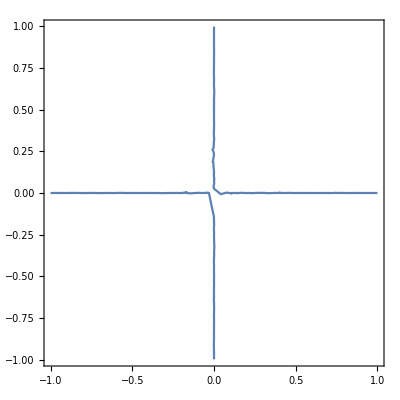

```mathematica
ContourPlot[Sin[x y]==0,{x,y}∈Disk[]]
```

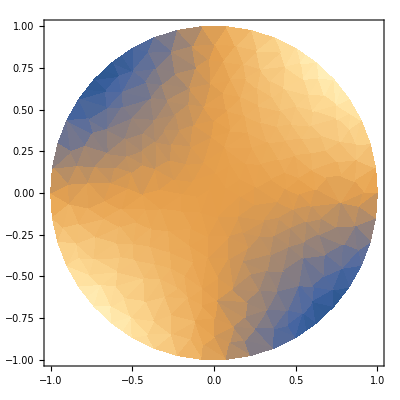

```mathematica
DensityPlot[Sin[x y]==0,{x,y}∈Disk[]]
```

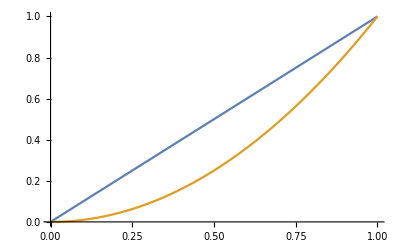

```mathematica
Plot[{x,x^2},{x,0,1}]
```

```mathematica
Cross[{x,x,0},{x,x^2,0}]
```

{0,0,-x^2+x^3}

```mathematica
Cross[D[{x,x,0}, x],D[{x,x^2,0}, x]]
```

{0,0,-1+2 x}

```mathematica
FullSimplify[ArcCurvature[{x,x^2},x],x∈Reals]
```

2/((1+4 x^2)^(3/2))

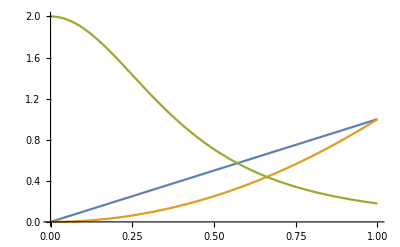

```mathematica
Plot[{x,x^2,2/((1+4 x^2)^(3/2))},{x,0,1}]
```

```mathematica
FullSimplify[Normalize[D[{x,x}, x]].Normalize[D[{x,x^2}, x]],x∈Reals]
```

(1+2 x)/(√(2+8 x^2))

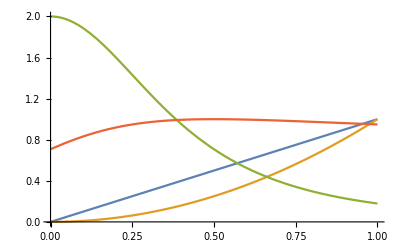

```mathematica
Plot[{x,x^2,2/((1+4 x^2)^(3/2)),(1+2 x)/(√(2+8 x^2))},{x,0,1}]
```

```mathematica
FullSimplify[Identity[D[{x,x}, x]].Identity[D[{x,x^2}, x]],x∈Reals]
```

1+2 x

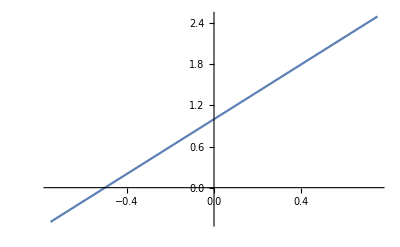

```mathematica
Plot[1+2 x,{x,-0.75,0.75}]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],x∈Reals]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f[x],f'[x],f''[x]}∈Reals]
```

Abs[f''[x]]/((1+f'[x]^2)^(3/2))

```mathematica
Abs[f''[x]]/((1+f'[x]^2)^(3/2))√(1+f'[x]^2)
```

Abs[f''[x]]/(1+f'[x]^2)

```mathematica
With[{f=Identity},
Abs[f''[x]]/(1+f'[x]^2)
]
```

0

```mathematica
With[{f=# #&},
Abs[f''[x]]/(1+f'[x]^2)
]
```

2/(1+4 x^2)

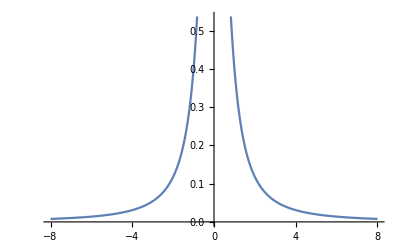

```mathematica
Plot[2/(1+4 x^2),{x,-8,8}]
```

```mathematica
Integrate[√(1+4 x^2),x]
```

1/2 x √(1+4 x^2)+1/4 ArcSinh[2 x]

```mathematica
Integrate[f[x],x]==1/2 x f[x]+1/4 ArcSinh[2 x]
```

∫f[x]ⅆx==1/4 ArcSinh[2 x]+1/2 x f[x]

```mathematica
Reduce[∫f[x]ⅆx==1/4 ArcSinh[2 x]+1/2 x f[x]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[∫f[x]ⅆx==1/4 ArcSinh[2 x]+1/2 x f[x]]

```mathematica
ArcLength[{x,x},{x,0,1}]
```

√2

```mathematica
MinimalPolynomial[√2,x]
```

-2+x^2

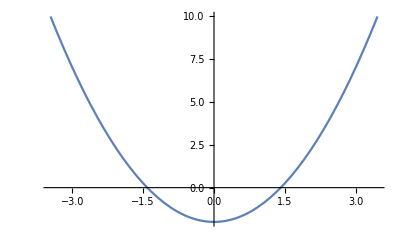

```mathematica
Plot[-2+x^2,{x,-3.464101615137755,3.464101615137755}]
```

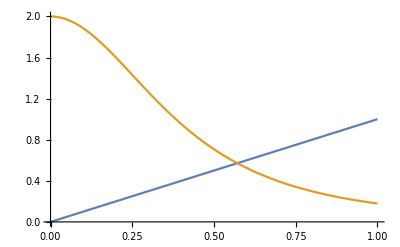

```mathematica
Plot[{x,2/((1+4 x^2)^(3/2))},{x,0,1}]
```

```mathematica
ArcLength[{x,x^2},{x,0,1}]
```

1/4 (2 √5+ArcSinh[2])